# Analysis of Triangle Completion Categorical experiment

## Loading the data and functions

```mathematica
SetDirectory["/home/uvhart/GitHubLib/EuclideanGeoSurvey"];
```

```mathematica
SetDirectory["/Users/alcarden4/Desktop/WebstormProjects/EuclideanGeoSurvey"]
```

/Users/alcarden4/Desktop/WebstormProjects/EuclideanGeoSurvey

```mathematica
Needs["ErrorBarPlots`"];
LogFilePilot1=DeleteCases[Import["logVertexCat.txt","Table"],Except[{___,"ERROR",___}]];
LogFileExp1=DeleteCases[Import["logVertexCatExp.txt","Table"],Except[{___,"ERROR",___}]];
```

#### Data

```mathematica
DataUnCln={LogFileExp1[[;;,;;2]],LogFileExp1[[;;,6;;]]}ᵀ;
DATA=Join[#[[1]],If[Length[#[[2]]]==1,StringSplit[#[[2,1]],"_"],Join[StringSplit[#[[2,1]],"_"],#[[2,2;;]]]]]&/@DataUnCln;
DATASort=Select[Select[GatherBy[DATA,#[[3]]&],Length@#>127&],#[[5,5]]≠"9999"&];
DataClean={Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},SortBy[#,#[[{1,2}]]&]&@GatherBy[Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]],#[[{1,2}]]&]}&/@DATASort;
(*ID,gender,age,right/left handed,education*)
(*7=angle; 9=base factor; 11=Qtype; 12=Manipulation; 13=What's manipulated; 15=correct answer; 17=timing; 19=user answer;*)
DataClnGraded=Join@@@Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataClean[[;;,2]],{3}];
```

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
QuestionType={"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"};
AnswerRules={"downward"-> 1,"stayPlace"-> 2,"upward"-> 3,"smaller"-> 1,"same"-> 2,"bigger"-> 3};
```

DataClean

All questions together

```mathematica
DataCleanAll=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
DataCleanAllGraded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanAll[[;;,2]],{2}];
```

## Percent Correct

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

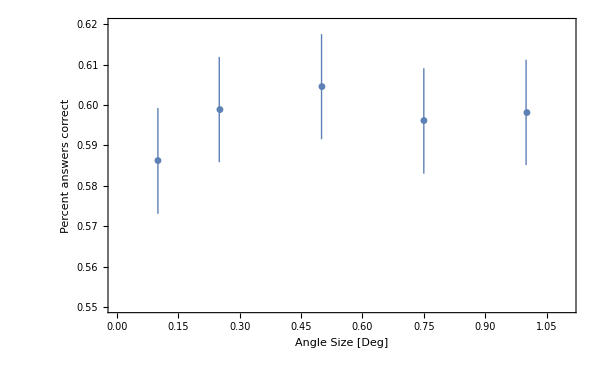

```mathematica
ErrorListPlot[#,PlotRange->{{0,1.1},{0.55,0.62}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])
```

### Percent correct vs. Angle Size

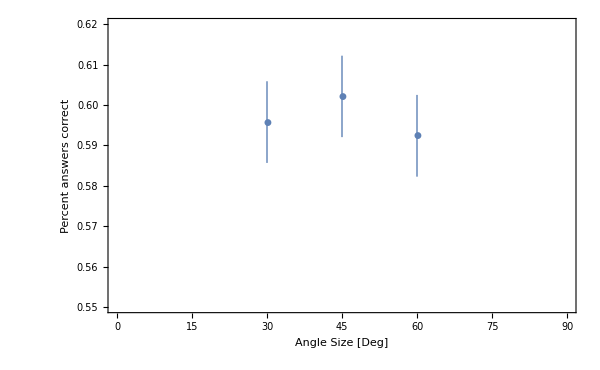

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{0.55,0.62}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[1]],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])
```

### Percent correct vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

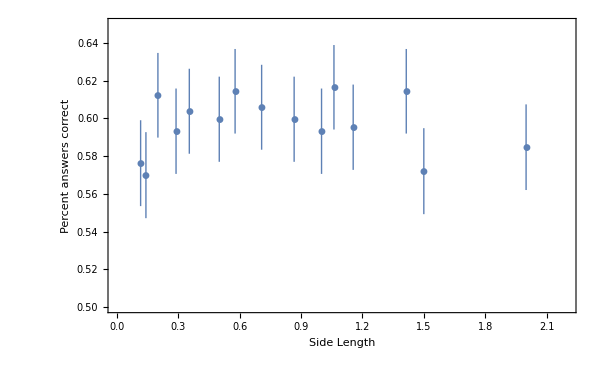

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0.5,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@#[[-1]]}&,DataCleanAllGraded,{2}],First])
```

### Percent correct vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (people get better vertex location than angle estimations)

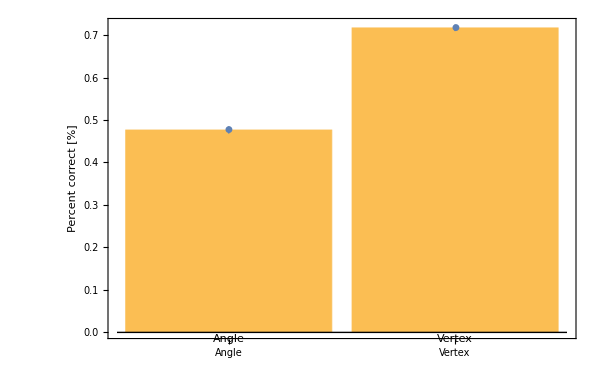

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])],First]
```

#### What’s being manipulated (angle manipulation easier than distance manipulations)

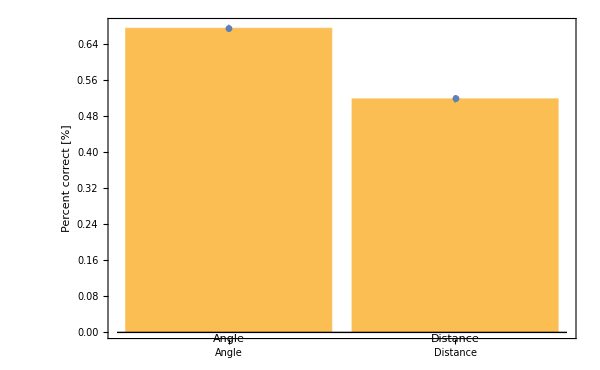

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])],First]
```

#### What’s being manipulated (no difference for increase/decrease)

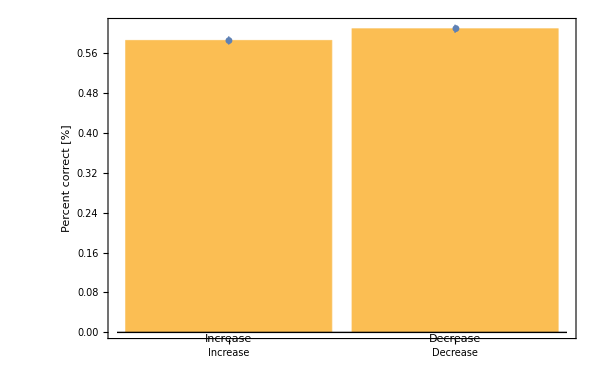

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@#[[-1]]}&,DataCleanAllGraded,{2}],First])],First]
```

#### Every Question Type Alone (easiest -> vertex and angle change, hardest->angles when distance changes)

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

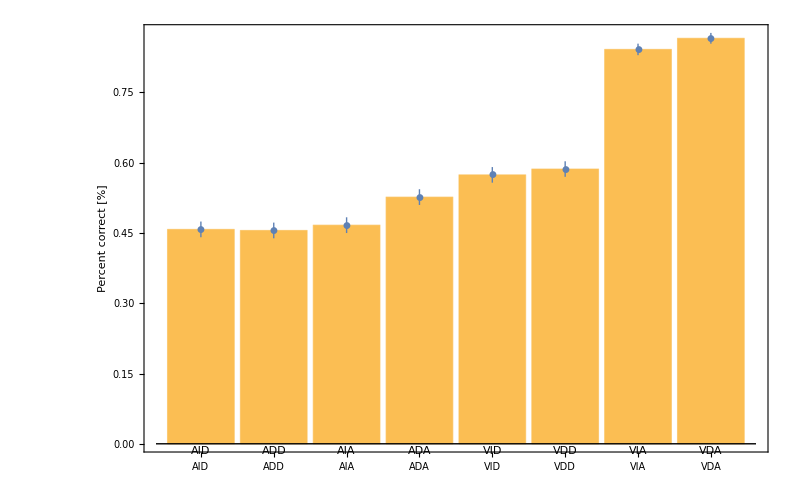

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@#[[-1]]}&,DataCleanAllGraded,{2}]/.rules,First])],First]
```

```mathematica
AnswerRules={"downward"-> 1,"stayPlace"-> 2,"upward"-> 3,"smaller"-> 1,"same"-> 2,"bigger"-> 3};
```

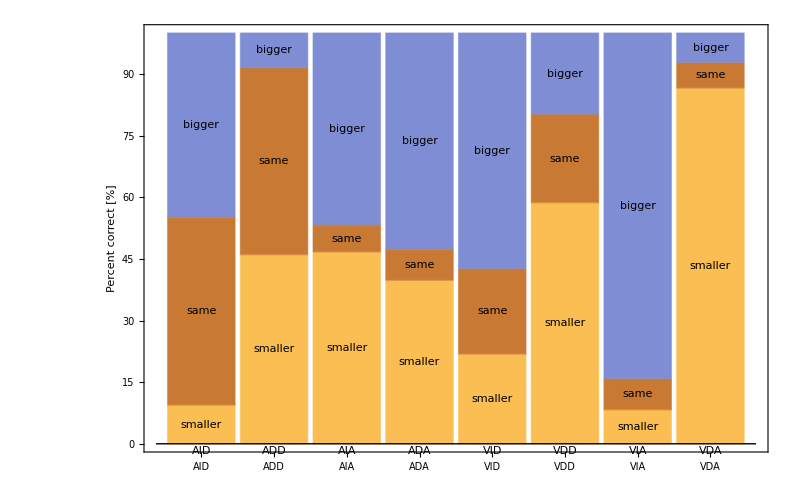

```mathematica
BarChart[#[[;;,2]],ChartLayout->"Percentile",ChartLabels->{{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},{"smaller","same","bigger"}},Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->18]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->800]&@SortBy[{#[[1,1]],SortBy[Tally[#[[;;,2]]],First][[;;,2]]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],#[[8]]/.AnswerRules}&,DataCleanAllGraded,{2}]/.rules,First]),First]
```

## Response times

### Response times vs. Base length (perhaps a slight dependence on base length)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

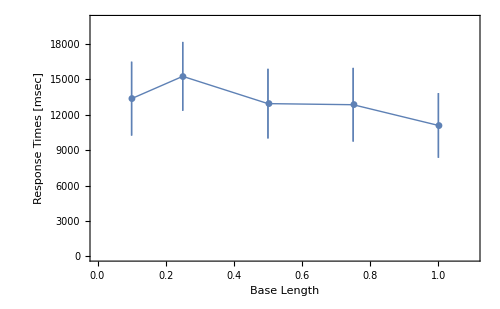

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])
```

### Response Times vs. Angle Size (mean - slight angle size dependence, median - no dependence on angle size)

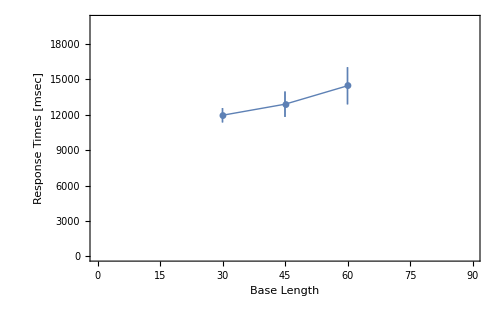

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First],First])
```

```mathematica
MannWhitneyTest[SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First],First][[{1,3},;;,2]]]
```

0.206885

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

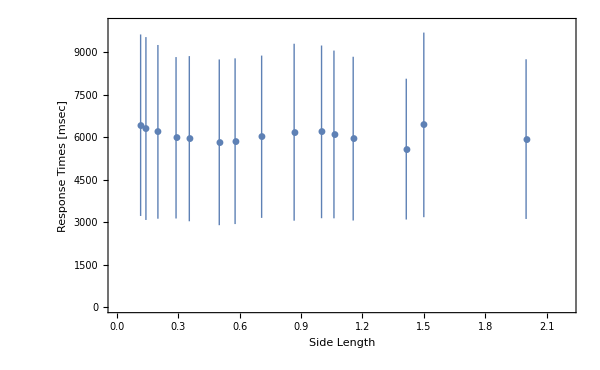

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,10 10^3}},Frame-> {True,True,False,False},FrameStyle-> 20,ImageSize-> 600,FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])
```

### Response Time vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (Angle is significantly longer than vertex)

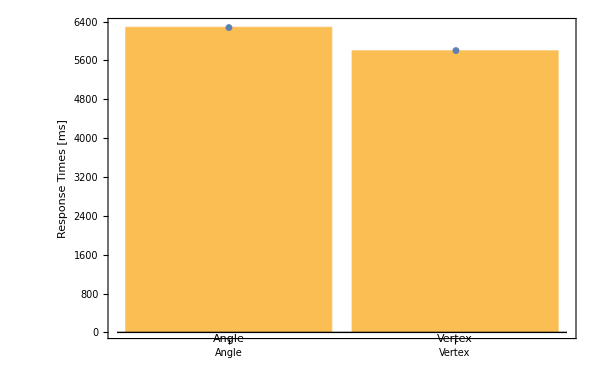

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Response Times [ms]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]]
```

0.0152242

#### What’s being manipulated (no difference between changes of angle and changes of distance)

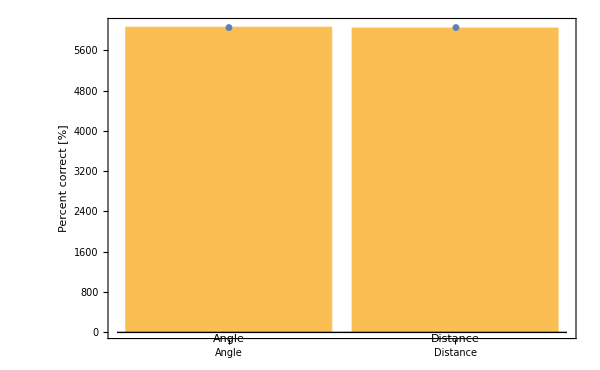

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]]
```

0.589352

#### What’s the manipulation - Increase/Decrease

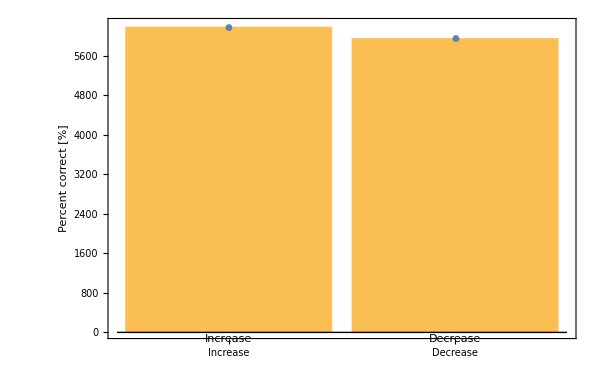

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]]
```

0.149468

#### Every Question Type Alone

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

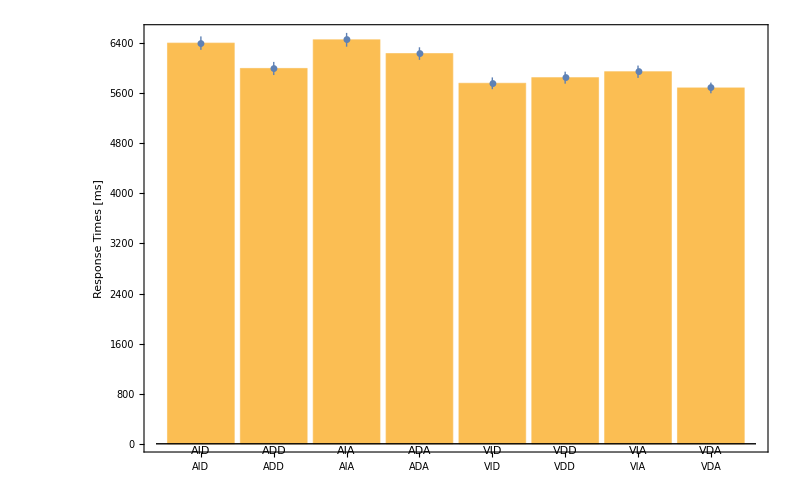

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]) ]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}]/.rules,First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGraded,{2}]/.rules,First]),First][[{7,8},;;,2]])
```

0.140093

## Only Angle Increase and Decrease Distance (AID and ADD)

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

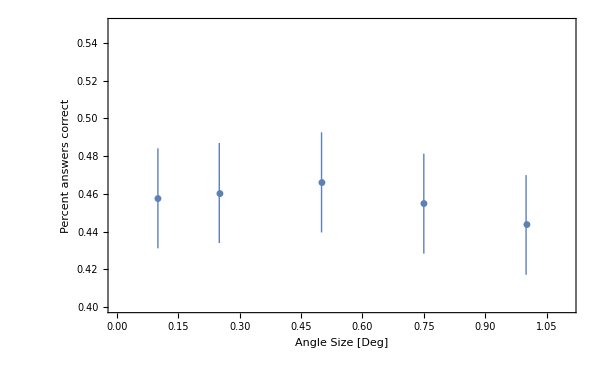

```mathematica
ErrorListPlot[#,PlotRange->{{0,1.1},{0.4,0.55}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@#[[-1]]}&,Select[#,(#[[3]]=="angle"&&#[[5]]=="distance")&]&/@DataCleanAllGraded,{2}],First])
```

### Percent correct vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

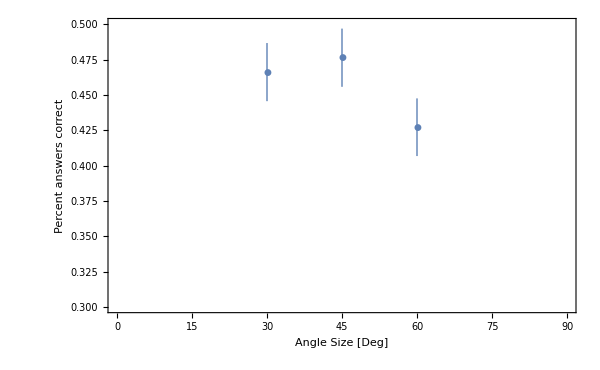

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{0.3,0.5}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[1]],N@#[[-1]]}&,Select[#,(#[[3]]=="angle"&&#[[5]]=="distance")&]&/@DataCleanAllGraded,{2}],First])
```

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

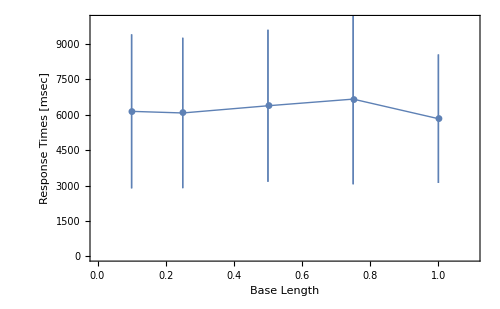

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,10 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@ToExpression@#[[7]]}&,Sort@Select[#,(#[[3]]=="angle"&&#[[5]]=="distance")&]&/@DataCleanAllGraded,{2}],First])
```

### Response times vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

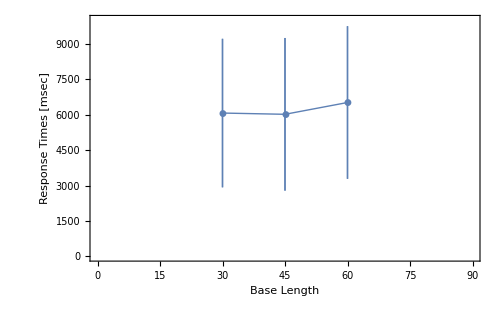

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0,10 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,Sort@Select[#,(#[[3]]=="angle"&&#[[5]]=="distance")&]&/@DataCleanAllGraded,{2}],First])
```

## Analysis per Question Type

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

```mathematica
DataPerQTypeAll=(Sort@GatherBy[Join@@Map[{#[[3;;5]]/.rules,#[[{1,2,7,8,9}]]}&,DataCleanAllGraded,{2}],First])[[;;,;;,2]];
QuestionType={"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"};
```

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

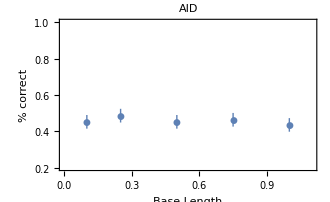
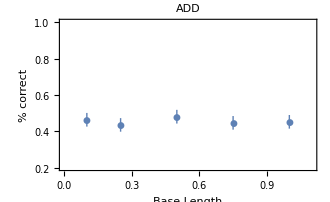
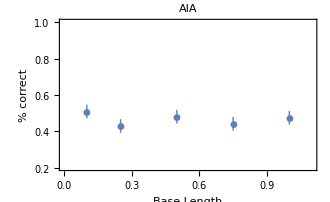
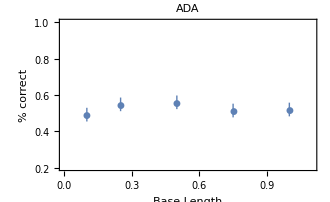
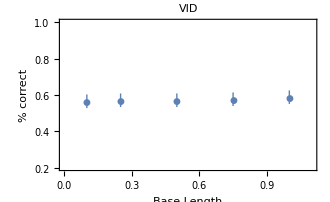
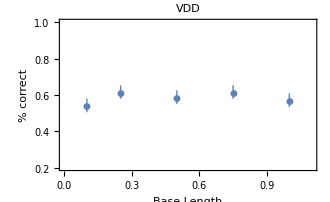
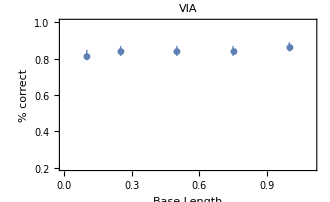
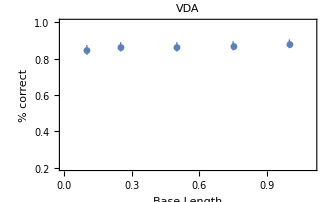

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,1.1},{0.2,1}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,1.1},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.3},0.2,1},{{PerHigh,0.8},0.4,1}]
```

Part::partd: Part specification DataPerQTypeAll⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAll⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Percent correct vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

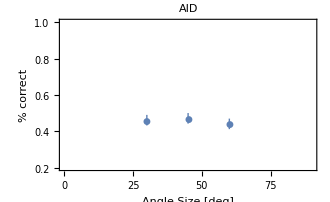
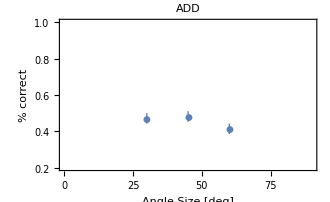
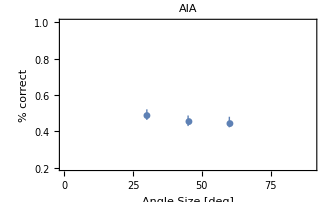
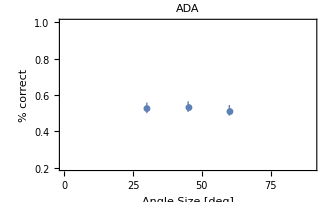
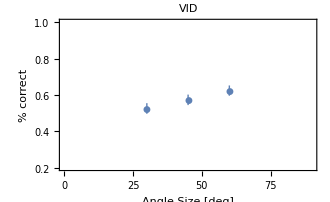
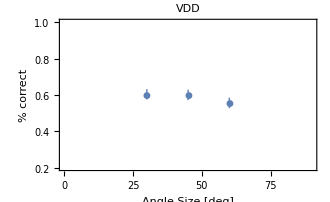
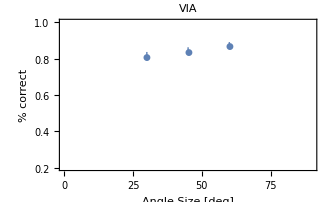
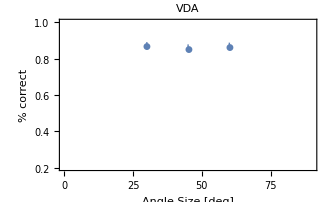

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,90},{0.2,1}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,90},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.3},0.2,1},{{PerHigh,0.8},0.4,1}]
```

Part::partd: Part specification DataPerQTypeAll⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAll⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

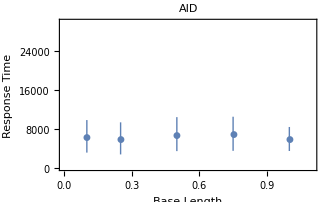
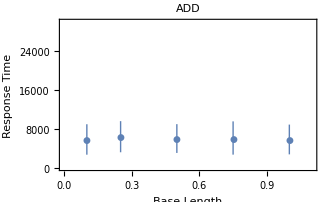
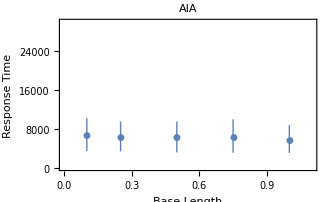
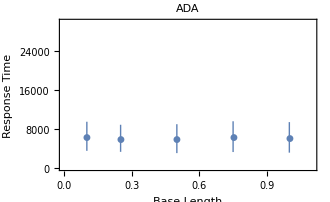
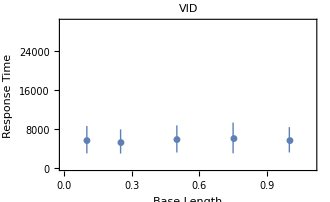
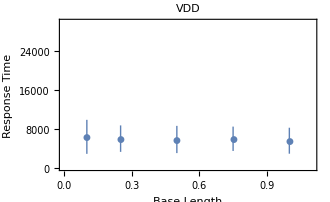
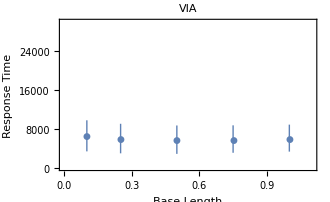
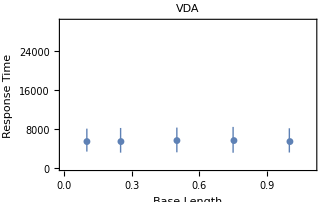

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,1.1},{0,30 10^3}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Time"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeAll,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,1.1},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,10},8,40},{f,{Median,Mean}}]
```

Part::partd: Part specification DataPerQTypeAll⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAll⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Response times vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

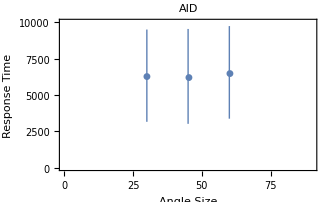
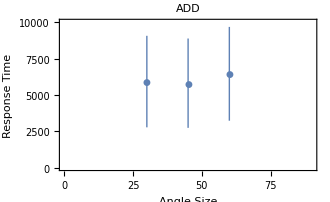
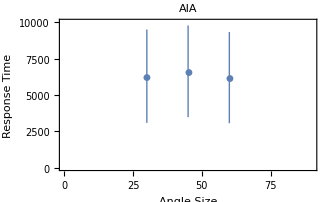
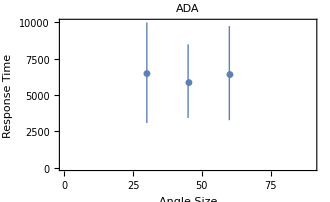
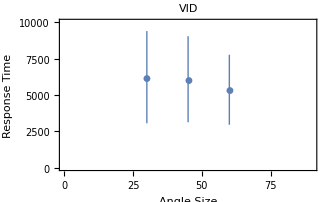
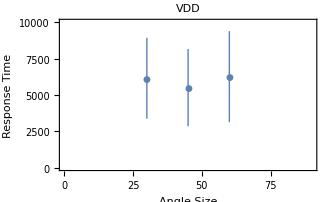
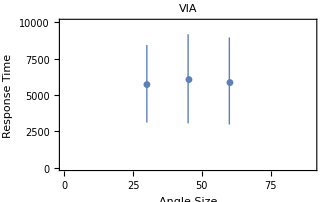
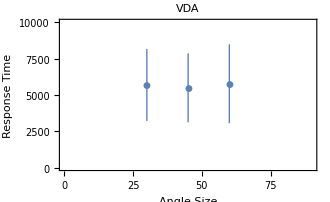

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,90},{0,10 10^3}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Time"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeAll,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,90},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,10},8,40},{f,{Median,Mean}}]
```

Part::partd: Part specification DataPerQTypeAll⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAll⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

## Learning effect

```mathematica
DataCleanFirst40=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#[[;;46]],StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
DataCleanLast40=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#[[-44;;]],StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
DataCleanAll=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
```

```mathematica
DataCleanFirst40Graded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanFirst40[[;;,2]],{2}];
DataCleanLast40Graded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanLast40[[;;,2]],{2}];
DataCleanAllGraded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanAll[[;;,2]],{2}];
```

### Change in response times (first 40 vs. last 40)

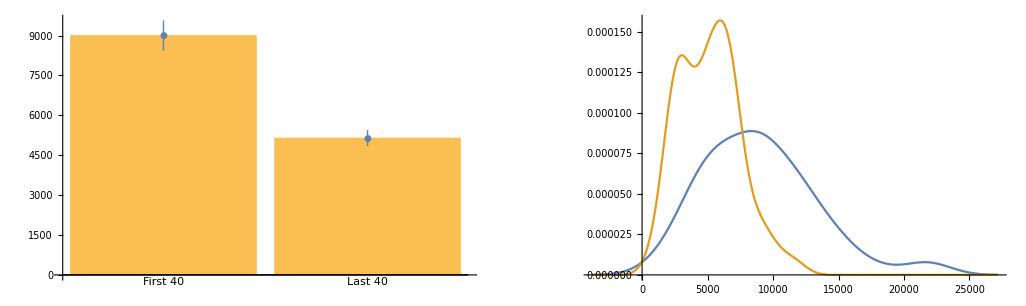

```mathematica
GraphicsRow@{Show[BarChart[#[[;;,1]],ChartLabels->{"First 40","Last 40"}],ErrorListPlot[#,PlotStyle->Thick,PlotMarkers->Automatic]]&@(N@{Mean@#,(StandardDeviation@#)/(Sqrt@Length@#)}&/@{Median/@ToExpression@DataCleanFirst40Graded[[;;,;;,7]],Median/@ToExpression@DataCleanLast40Graded[[;;,;;,7]]}),SmoothHistogram@{Median/@ToExpression@DataCleanFirst40Graded[[;;,;;,7]],Median/@ToExpression@DataCleanLast40Graded[[;;,;;,7]]}}
```

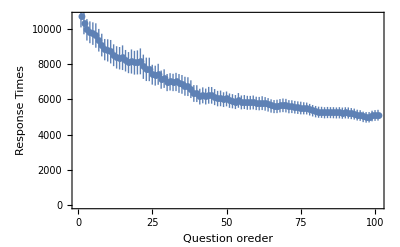

```mathematica
ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"Question oreder","Response Times"},PlotStyle->Thick,PlotMarkers->Automatic]&@(N@({Mean@#,(StandardDeviation@#)/(Sqrt@Length@#)}&@(Median/@Partition[#,20,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,7]])))ᵀ)
```

```mathematica
Manipulate[ListPlot[#[[i]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Question order","Response Time [ms]"}]&@(N@(Median/@Partition[#,20,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,7]]))),{i,1,Length@DataCleanAllGraded,1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

ListPlot::lpn: $Failed⟦1⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Change in percent correct (first 40 vs. last 40)

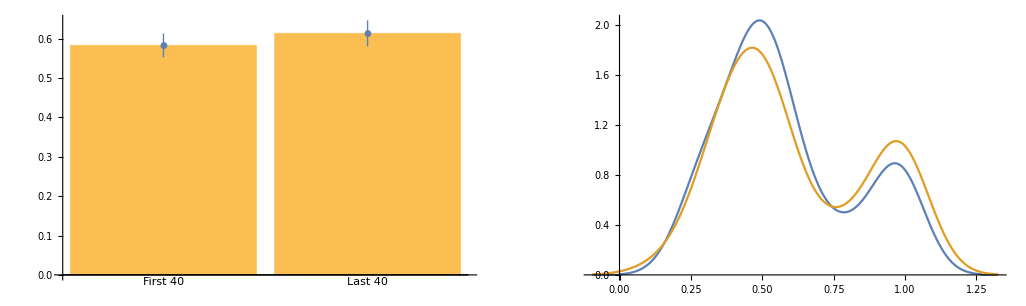

```mathematica
GraphicsRow@{Show[BarChart[#[[;;,1]],ChartLabels->{"First 40","Last 40"}],ErrorListPlot[#,PlotStyle->Thick,PlotMarkers->Automatic]]&@(N@{Mean@#,(StandardDeviation@#)/(Sqrt@Length@#)}&/@{Mean/@ToExpression@DataCleanFirst40Graded[[;;,;;,-1]],Mean/@ToExpression@DataCleanLast40Graded[[;;,;;,-1]]}),SmoothHistogram@{Mean/@ToExpression@DataCleanFirst40Graded[[;;,;;,-1]],Mean/@ToExpression@DataCleanLast40Graded[[;;,;;,-1]]}}
```

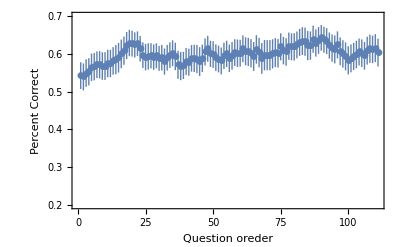

```mathematica
ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"Question oreder","Percent Correct"},PlotStyle->Thick,PlotMarkers->Automatic,PlotRange->{All,{0.2,0.7}}]&@(N@({Mean@#,(StandardDeviation@#)/(Sqrt@Length@#)}&@(Mean/@Partition[#,10,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,-1]])))ᵀ)
```

```mathematica
Manipulate[,{i,1,Length@DataCleanAllGraded,1}]
```

```mathematica
Manipulate[GraphicsRow[{ListPlot[#[[i]],Joined->True,PlotRange->{All,{0,1}},Frame->True,FrameLabel->{"Question order","Percent Correct"}]&@(N@(Mean/@Partition[#,10,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,-1]]))),ListPlot[#[[i]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Question order","Response Time [ms]"}]&@(N@(Median/@Partition[#,10,1]&/@(ToExpression@DataCleanAllGraded[[;;,;;,7]])))},ImageSize->800],{i,1,Length@DataCleanAllGraded,1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦59⟧ is longer than depth of object.

ListPlot::lpn: $Failed⟦59⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦59⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦59⟧ is longer than depth of object.

ListPlot::lpn: $Failed⟦59⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦59⟧ is longer than depth of object.

First X questions analysis

```mathematica
FirstXQuest=20;
```

```mathematica
DataCleanAll=({Flatten@{#[[2,{3,5}]],#[[3,5]],#[[4,5]],#[[5,5]]},Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]]}&/@DATASort);
DataCleanAllGraded=Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataCleanAll[[;;,2]],{2}];
```

```mathematica
DataCleanFirstQ={DataCleanAll[[;;,1]],DataCleanAll[[;;,2,;;FirstXQuest]]}ᵀ;
DataCleanFirstQGraded=DataCleanAllGraded[[;;,;;FirstXQuest]];
```

## Percent Correct

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

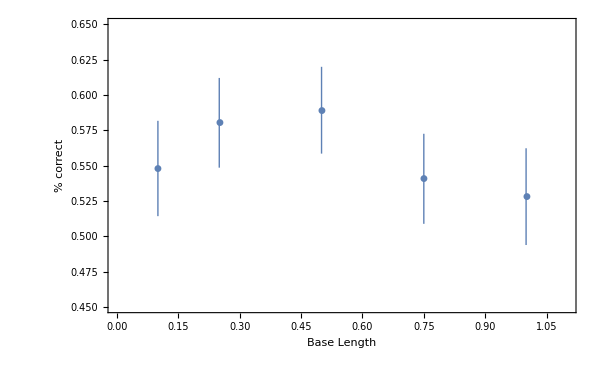

```mathematica
ErrorListPlot[#,PlotRange->{{0,1.1},{0.45,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@#[[-1]]}&,DataCleanFirstQGraded,{2}],First])
```

### Percent correct vs. Angle Size

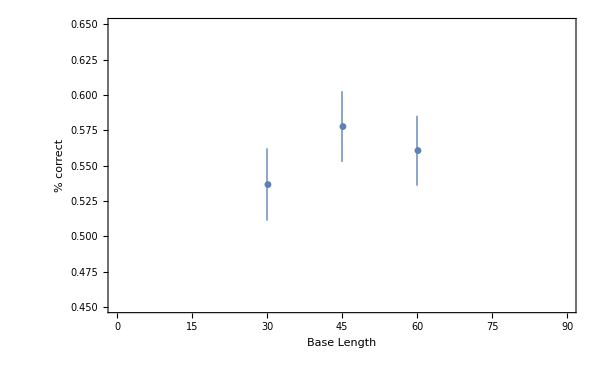

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{0.45,0.65}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[1]],N@#[[-1]]}&,DataCleanFirstQGraded,{2}],First])
```

### Percent correct vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

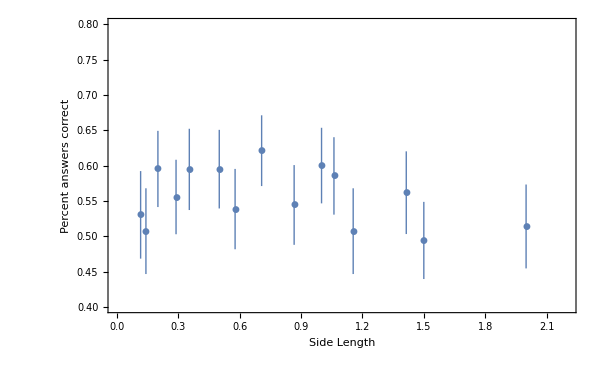

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0.4,0.8}},Frame-> {True,True,False,False},FrameStyle-> 20, ImageSize-> 600,FrameLabel->{"Side Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@#[[-1]]}&,DataCleanFirstQGraded,{2}],First])
```

### Percent correct vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about

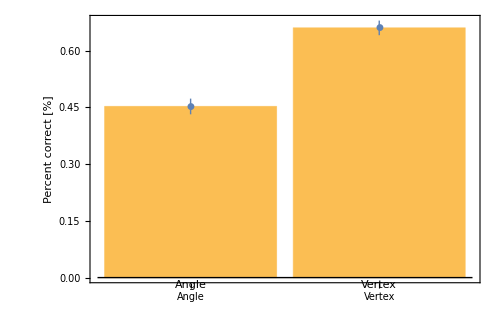

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize-> 500,BaseStyle->Directive[FontSize->20] ,FrameLabel->{None,"Percent correct [%]"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@#[[-1]]}&,DataCleanFirstQGraded,{2}],First])],First]
```

#### What’s being manipulated

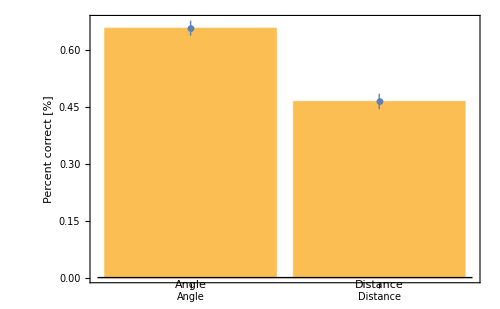

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize-> 500,BaseStyle->Directive[FontSize->20] ,FrameLabel->{None,"Percent correct [%]"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@#[[-1]]}&,DataCleanFirstQGraded,{2}],First])],First]
```

#### Type of change

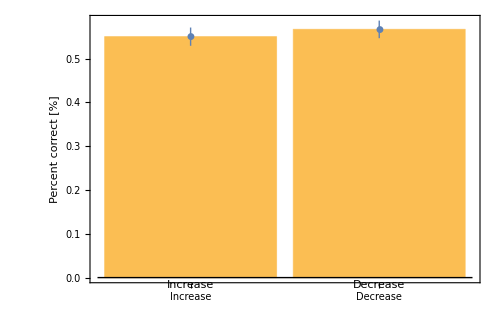

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize-> 500,BaseStyle->Directive[FontSize->20] ,FrameLabel->{None,"Percent correct [%]"}],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@#[[-1]]}&,DataCleanFirstQGraded,{2}],First])],First]
```

#### Every Question Type Alone (AID vs. ADD sig. not the same)

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

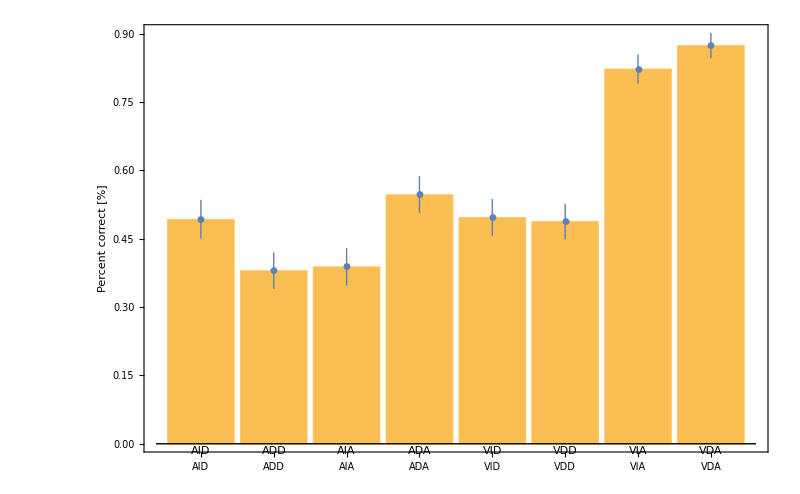

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20] ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@#[[-1]]}&,DataCleanFirstQGraded,{2}]/.rules,First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@#[[-1]]}&,DataCleanFirstQGraded,{2}]/.rules,First]),First][[{1,2}]])
```

3.09391×10^-63

```mathematica
AnswerRules={"downward"-> 1,"stayPlace"-> 2,"upward"-> 3,"smaller"-> 1,"same"-> 2,"bigger"-> 3};
```

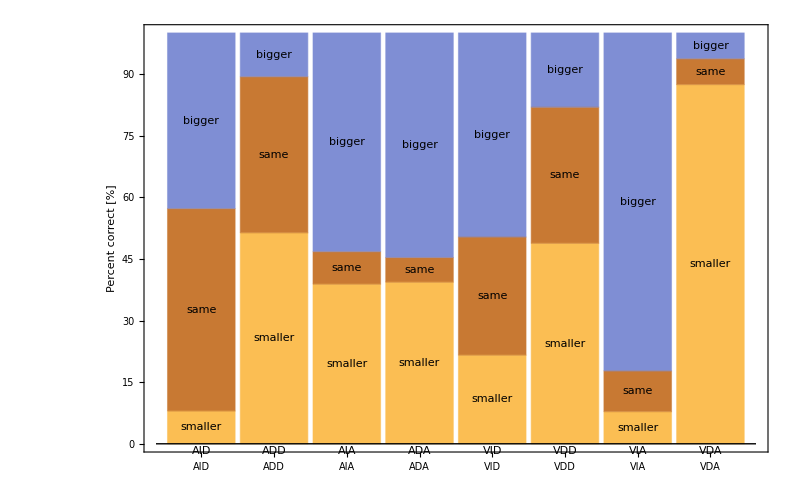

```mathematica
BarChart[#[[;;,2]],ChartLayout->"Percentile",ChartLabels->{{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},{"smaller","same","bigger"}},Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->18]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->800]&@SortBy[{#[[1,1]],SortBy[Tally[#[[;;,2]]],First][[;;,2]]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],#[[8]]/.AnswerRules}&,DataCleanFirstQGraded,{2}]/.rules,First]),First]
```

## Response times

### Response times vs. Base length (slight increase, not significant)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

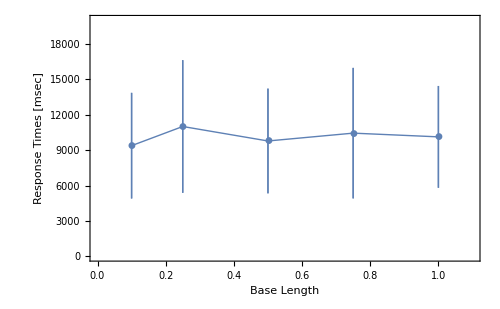

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])
```

### Response Times vs. Angle Size (angles do affect response times!)

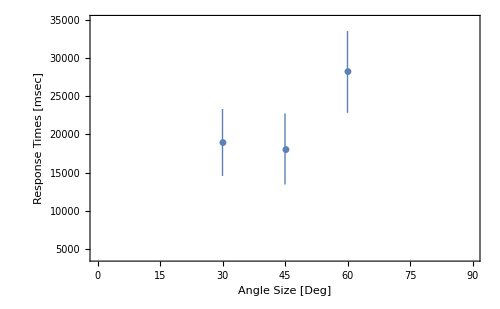

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{4 10^3,35 10^3}},Frame-> {True,True,False,False},FrameStyle-> 20,ImageSize-> 500,FrameLabel->{"Angle Size [Deg]","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[MedianDeviation[#[[;;,2]]]]}&/@GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])
```

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

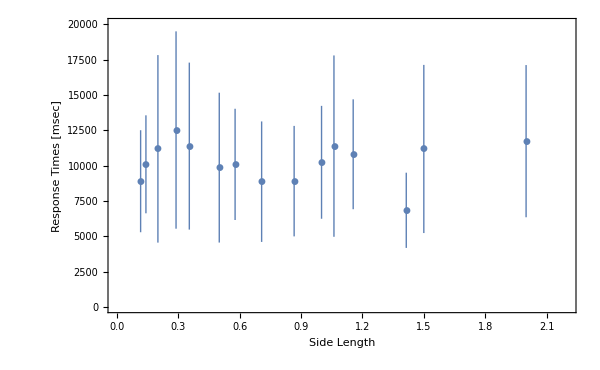

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 20,ImageSize-> 600,FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])
```

### Response Time vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (longer times for Angle determination than Vertex)

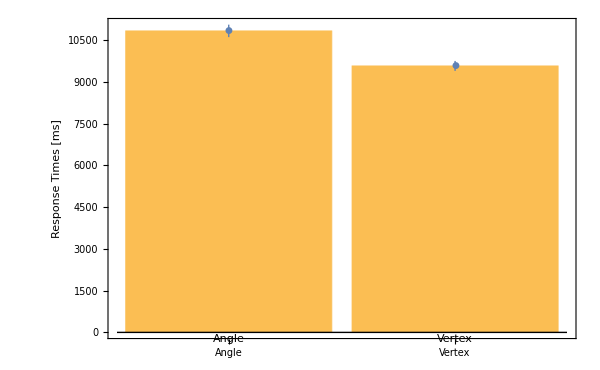

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Response Times [ms]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])[[;;,;;,2]]
```

0.00511897

#### What’s being manipulated

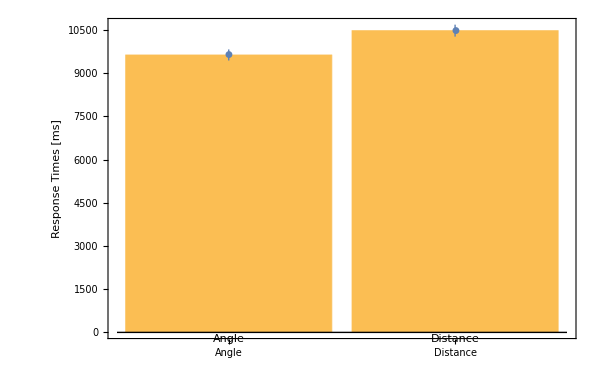

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])[[;;,;;,2]]
```

0.635405

#### Type of change (Median - the same, Mean - there is a difference between the increase (longer) and decrease (shorter)).

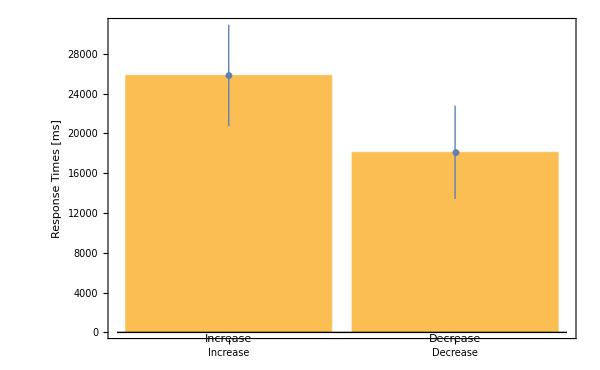

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Response Times"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}],First])[[;;,;;,2]]
```

0.215994

#### Every Question Type Alone (Median - inverse trend as the % correct, Mean - huge differences between increase angle/distance and decrease angle/distance)

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

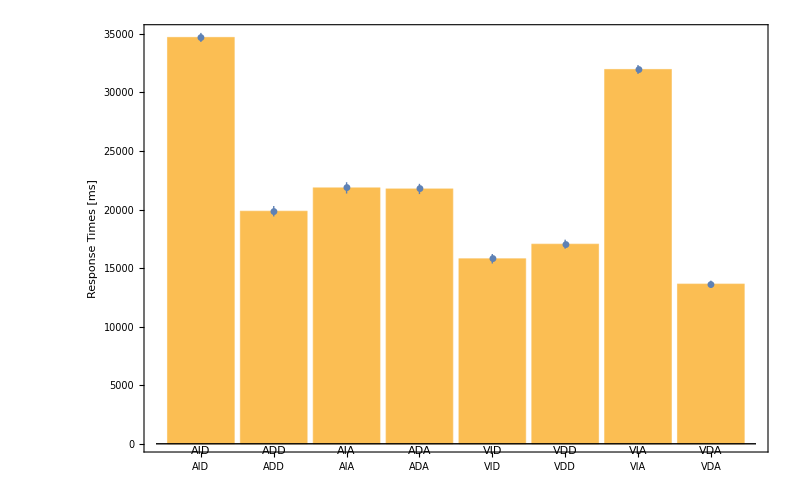

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]) ]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}]/.rules,First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanFirstQGraded,{2}]/.rules,First]),First][[{1,2},;;,2]])
```

0.329849

## Analysis per Question Type

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

```mathematica
DataPerQTypeFirstQ=(SortBy[GatherBy[Join@@Map[{#[[3;;5]]/.rules,#[[{1,2,7,8,9}]]}&,DataCleanFirstQGraded,{2}],First],#[[1,1]]&])[[;;,;;,2]];
QuestionType={"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"};
```

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

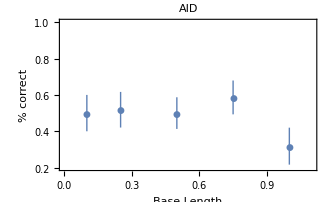
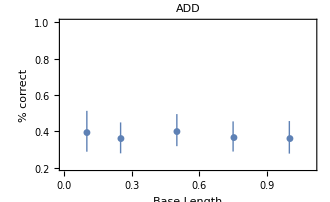
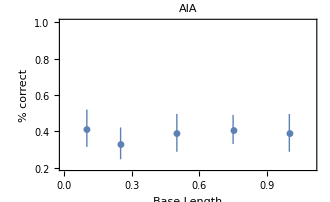
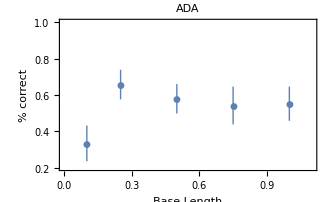
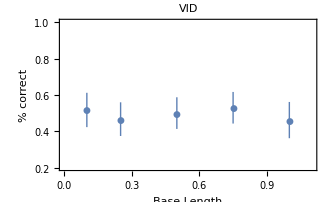
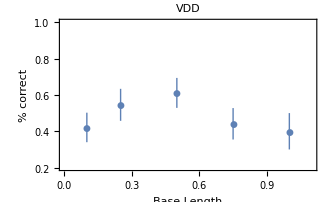
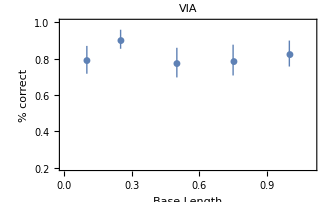
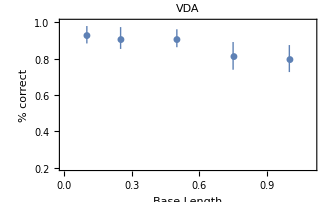

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,1.1},{0.2,1}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeFirstQ,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,1.1},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeFirstQ,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.2},0.2,1},{{PerHigh,0.8},0.4,1}]
```

Part::partd: Part specification DataPerQTypeFirstQ⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeFirstQ⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Percent correct vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

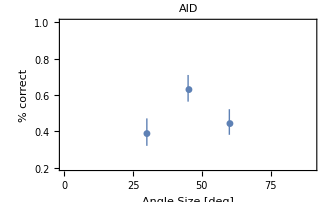
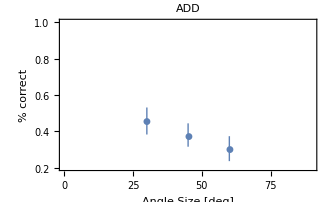
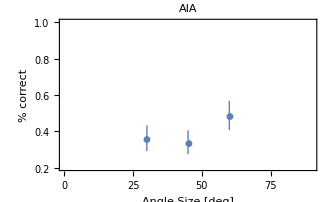
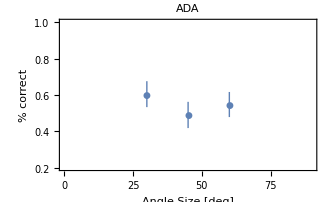
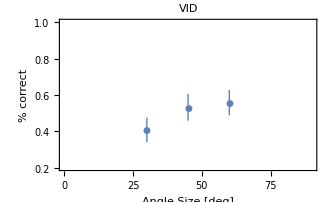
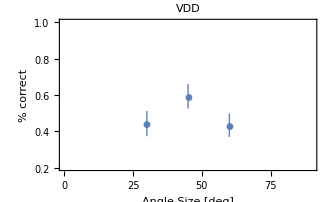
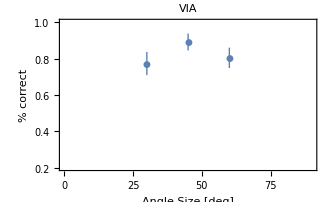
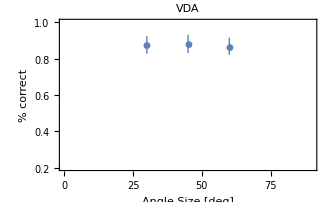

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,90},{0.2,1}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeFirstQ,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,90},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeFirstQ,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.2},0.2,1},{{PerHigh,0.8},0.4,1}]
```

Part::partd: Part specification DataPerQTypeFirstQ⟦{5,6}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeFirstQ⟦{5,6}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

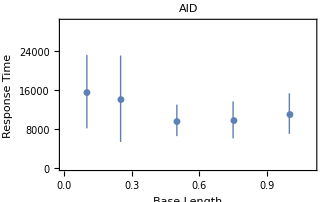
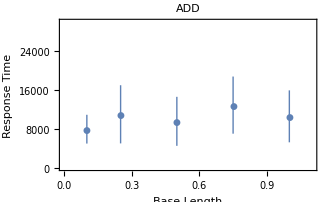
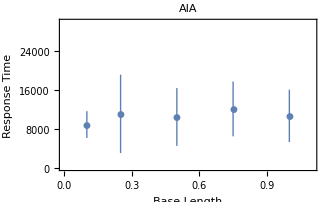
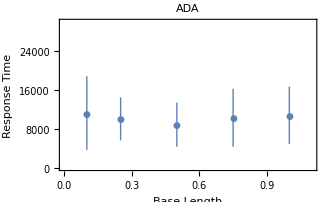
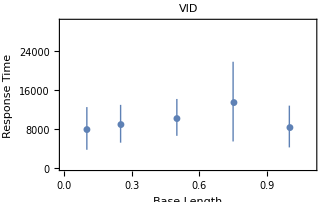
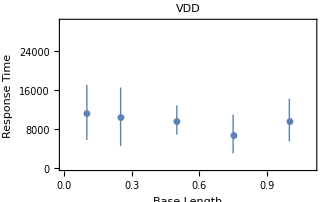
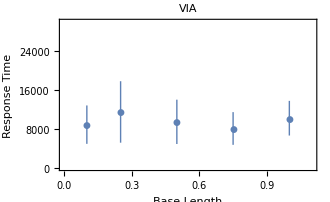
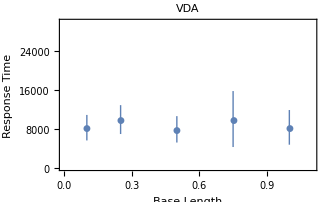

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,1.1},{0,30 10^3}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Time"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeFirstQ,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,1.1},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeFirstQ,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,20},8,40},{f,{Median,Mean}}]
```

Part::partd: Part specification DataPerQTypeFirstQ⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeFirstQ⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Response times vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

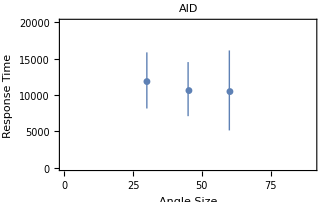
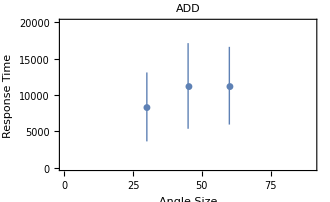
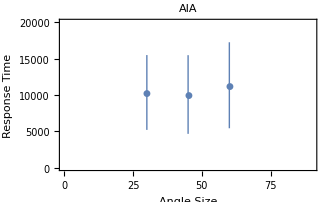
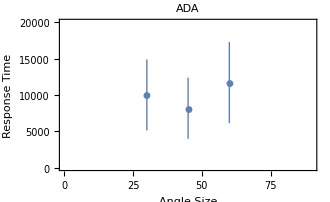
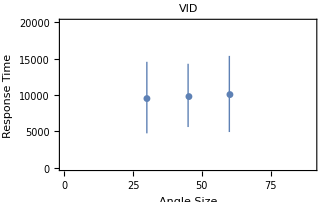
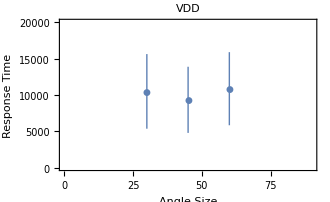
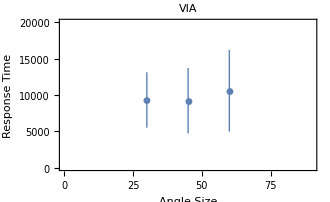
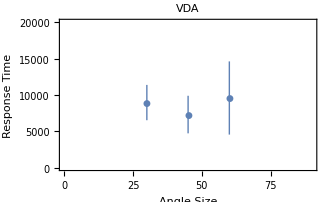

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,90},{0,20 10^3}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Time"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeFirstQ,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,90},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeFirstQ,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,20},8,80},{f,{Median,Mean}}]
```

Part::partd: Part specification DataPerQTypeFirstQ⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeFirstQ⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

## Only Angle Increase and Decrease Distance (AID and ADD)

### Percent correct vs. Base length (increase in base length - decrease in correct answers)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

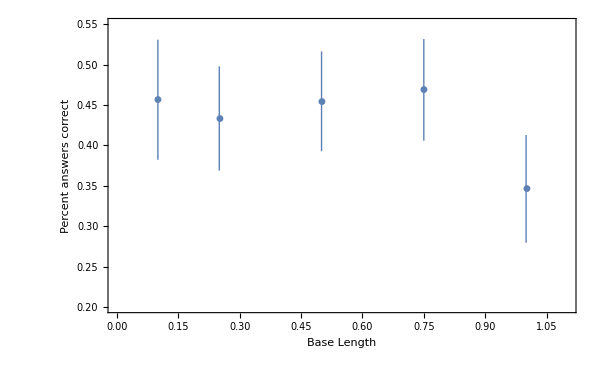

```mathematica
ErrorListPlot[#,PlotRange->{{0,1.1},{0.2,0.55}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@#[[-1]]}&,Select[#,(#[[3]]=="angle"&&#[[5]]=="distance")&]&/@DataCleanFirstQGraded,{2}],First])
```

### Percent correct vs. Angle Size (large angle size - less correct results)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

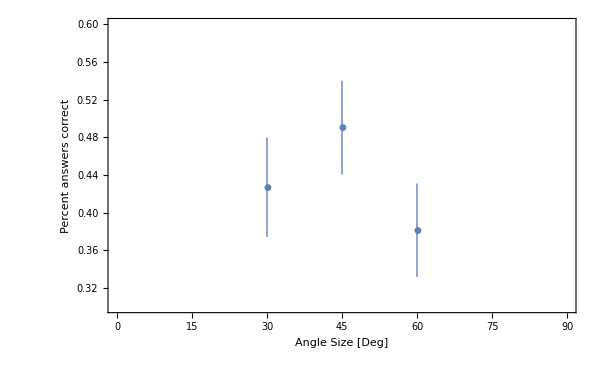

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{0.3,0.6}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[1]],N@#[[-1]]}&,Select[#,(#[[3]]=="angle"&&#[[5]]=="distance")&]&/@DataCleanFirstQGraded,{2}],First])
```

### Response times vs. Base length (mean - as base length increases response time increase, median - not so..)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

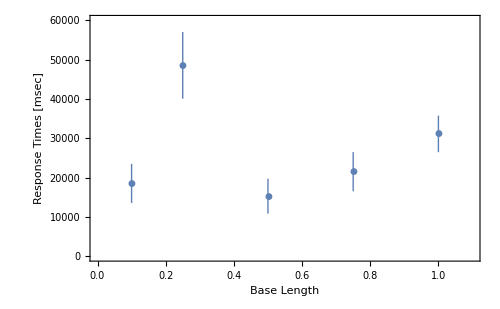

```mathematica
ErrorListPlot[#,PlotRange->{{0,1.1},{0,60 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@ToExpression@#[[7]]}&,Sort@Select[#,(#[[3]]=="angle"&&#[[5]]=="distance")&]&/@DataCleanFirstQGraded,{2}],First])
```

### Response times vs. Angle Size (mean - angle size increase -> response times increase, median - not so...)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

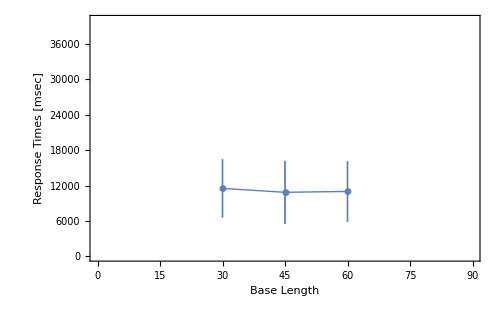

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0,40 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,Sort@Select[#,(#[[3]]=="angle"&&#[[5]]=="distance")&]&/@DataCleanFirstQGraded,{2}],First])
```

Experts vs. Leute

```mathematica
ExpTH=0.8;
DataCleanAllGradedExperts=Select[DataCleanAllGraded,Mean[#[[;;,-1]]]>ExpTH&];
DataCleanAllGradedNonExperts=Select[DataCleanAllGraded,Mean[#[[;;,-1]]]≤ ExpTH&];
```

## Percent Correct

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

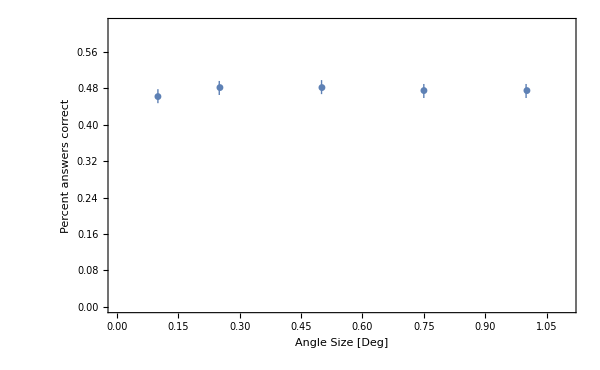

```mathematica
ErrorListPlot[#,PlotRange->{{0,1.1},{0,0.62}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Percent correct vs. Angle Size

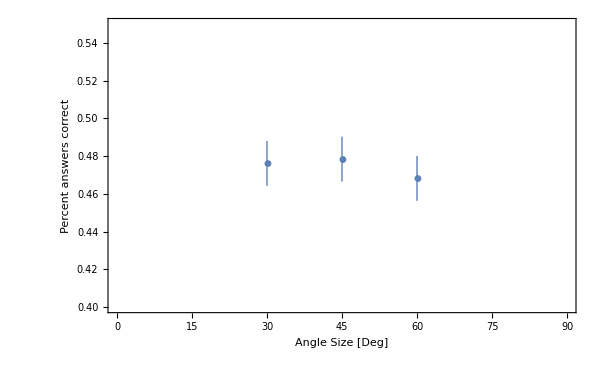

```mathematica
ErrorListPlot[#,PlotRange->{{0,90},{0.4,0.55}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
GatherBy[Join@@Map[{N@#[[1]],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Percent correct vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

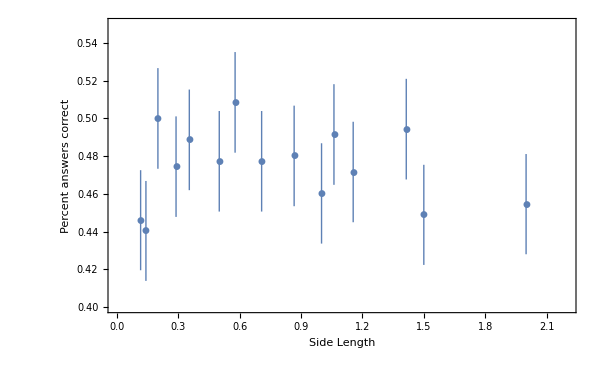

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0.4,0.55}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->20,ImageSize->600]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Percent correct vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (people get better vertex location than angle estimations)

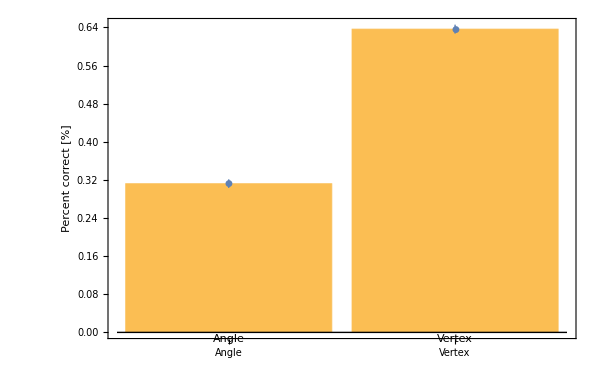

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

#### What’s being manipulated (angle manipulation easier than distance manipulations)

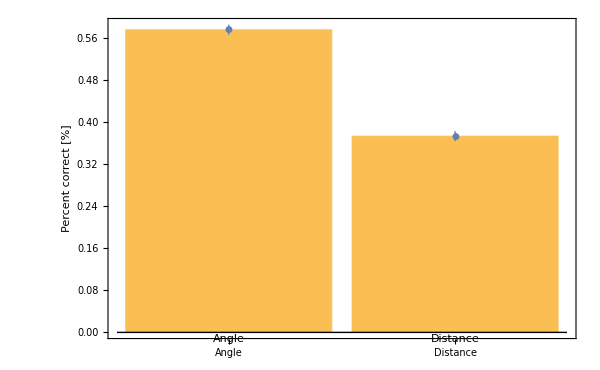

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

#### What’s being manipulated (significant difference between increase and decrease!!!)

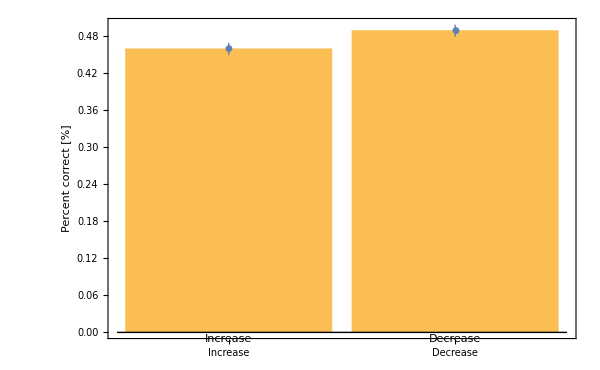

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Percent correct [%]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}],First][[;;,;;,2]])
```

0.0315916

#### Every Question Type Alone (easiest -> vertex and angle change, hardest->angles when distance changes)

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

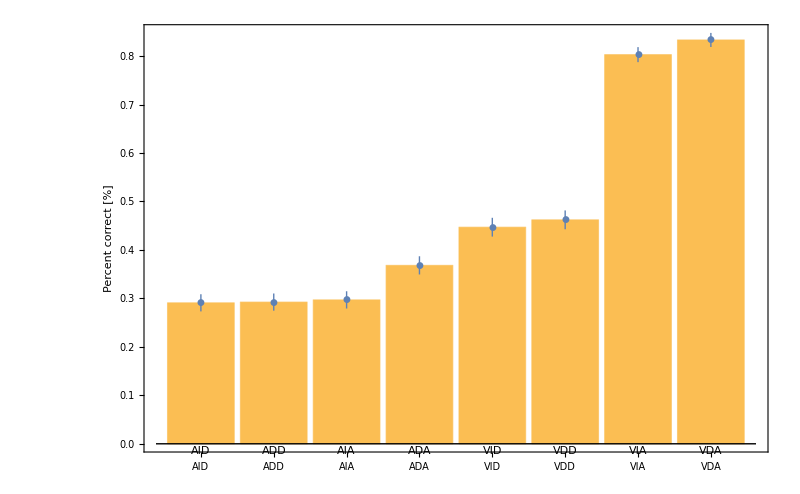

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Mean[#[[;;,2]]]},N@ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@#[[-1]]}&,DataCleanAllGradedNonExperts,{2}]/.rules,First])],First]
```

```mathematica
AnswerRules={"downward"-> 1,"stayPlace"-> 2,"upward"-> 3,"smaller"-> 1,"same"-> 2,"bigger"-> 3};
```

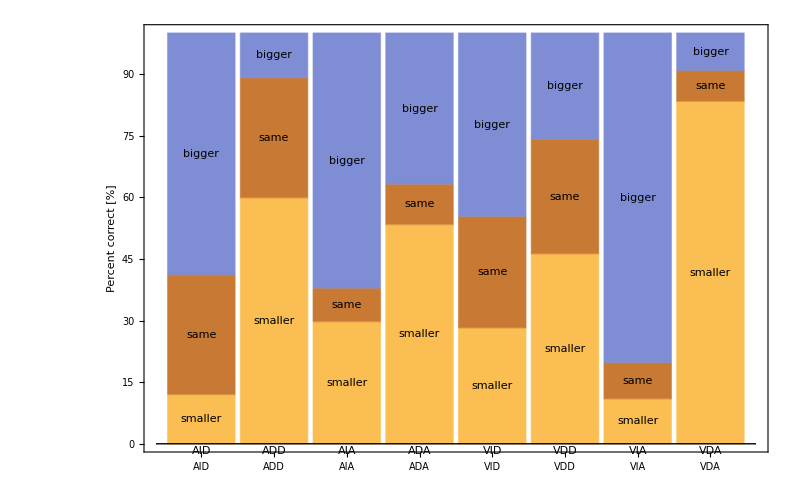

```mathematica
BarChart[#[[;;,2]],ChartLayout->"Percentile",ChartLabels->{{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},{"smaller","same","bigger"}},Frame-> {False,True,False,False},Axes->{True,False},BaseStyle->Directive[FontSize->18]
 ,FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->800]&@SortBy[{#[[1,1]],SortBy[Tally[#[[;;,2]]],First][[;;,2]]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],#[[8]]/.AnswerRules}&,DataCleanAllGradedNonExperts,{2}]/.rules,First]),First]
```

## Response times

### Response times vs. Base length (perhaps a slight dependence on base length)

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

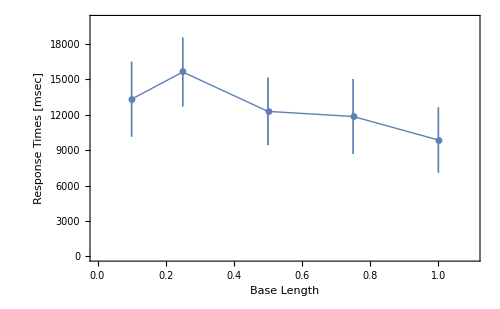

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@
GatherBy[Join@@Map[{N@#[[2]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Response Times vs. Angle Size (mean - slight angle size dependence, median - no dependence on angle size)

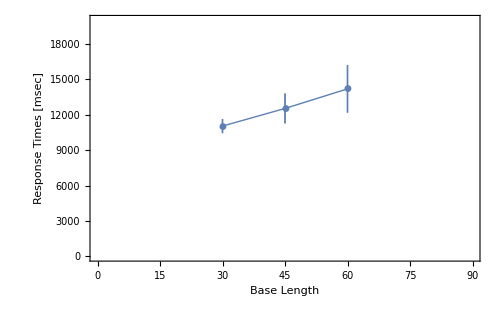

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 18,ImageSize-> 500,FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@
SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First],First])
```

```mathematica
MannWhitneyTest[SortBy[GatherBy[Join@@Map[{N@#[[1]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First],First][[{1,3},;;,2]]]
```

0.284882

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

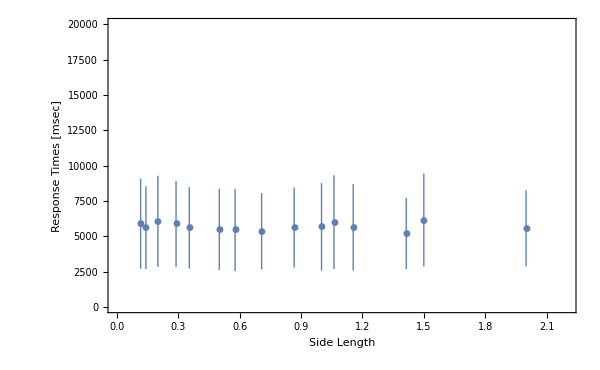

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,20 10^3}},Frame-> {True,True,False,False},FrameStyle-> 20,ImageSize-> 600,FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&/@GatherBy[Join@@Map[{N@((ToExpression@#[[2]])/Cos[ToExpression@#[[1]] Degree]),N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])
```

### Response Time vs. Question type

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

#### What’s being asked about (Angle is significantly longer than vertex)

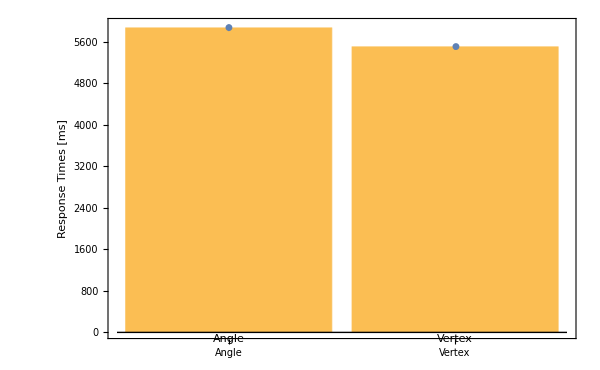

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Vertex"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->16],FrameLabel->{None,"Response Times [ms]"},FrameStyle->18,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[3]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.160393

#### What’s being manipulated (no difference between changes of angle and changes of distance)

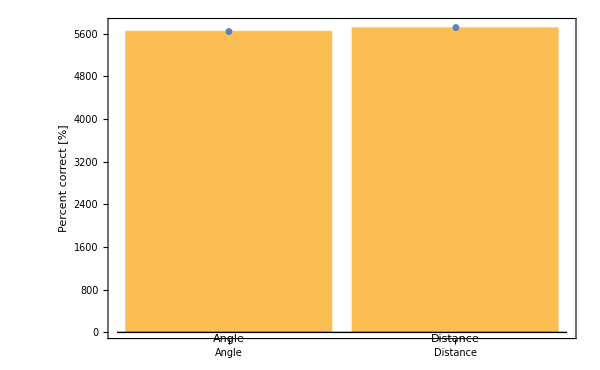

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Angle","Distance"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Percent correct [%]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[5]]=="angle",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.407871

#### What’s the manipulation - Increase/Decrease

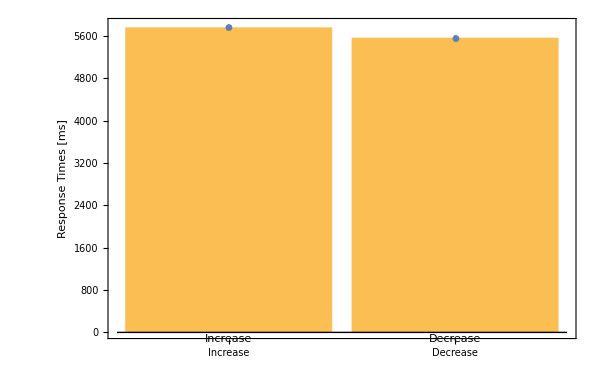

```mathematica
Show[BarChart[#[[;;,1,2]],ChartLabels->{"Increase","Decrease"},Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->18],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ImageSize->600],ErrorListPlot[#,Frame-> {True,True,False,False},FrameLabel->{"QuestionType [angle/vertex]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])],First]
```

```mathematica
MannWhitneyTest@(GatherBy[Join@@Map[{If[#[[4]]=="increase",1,2],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}],First])[[;;,;;,2]]
```

0.20998

#### Every Question Type Alone

```mathematica
rules={{"angle","increase","distance"}-> 1,{"angle","decrease","distance"}-> 2,{"angle","increase","angle"}-> 3,{"angle","decrease","angle"}->4,{"vertex","increase","distance"}->5,{"vertex","decrease","distance"}-> 6,{"vertex","increase","angle"}-> 7,{"vertex","decrease","angle"}-> 8};
```

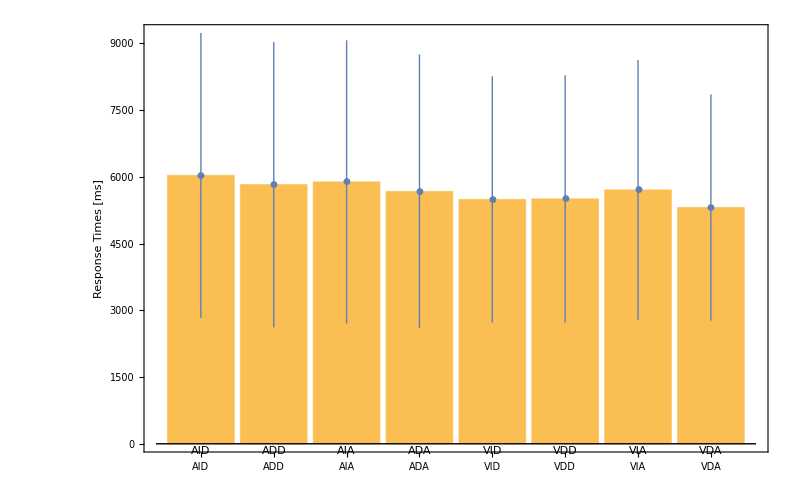

```mathematica
Show[BarChart[#[[;;,1,2]],Frame-> {False,True,False,False}
 ,Axes->{True,False},BaseStyle->Directive[FontSize->20],FrameLabel->{None,"Response Times [ms]"},FrameStyle->20,ChartLabels->{"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"},ImageSize->800],ErrorListPlot[#,Frame-> {True,True,False,False},PlotStyle->Thick,PlotMarkers->Automatic]]&@SortBy[Join[{{#[[1,1]],N@Median[#[[;;,2]]]},N@ErrorBar[MedianDeviation[#[[;;,2]]] ]}&/@(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}]/.rules,First])],First]
```

```mathematica
MannWhitneyTest@(SortBy[(GatherBy[Join@@Map[{#[[{3,4,5}]],N@ToExpression@#[[7]]}&,DataCleanAllGradedNonExperts,{2}]/.rules,First]),First][[{7,8},;;,2]])
```

0.287325

## Analysis per Question Type

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

```mathematica
DataPerQTypeAllNonExperts=(Sort@GatherBy[Join@@Map[{#[[3;;5]]/.rules,#[[{1,2,7,8,9}]]}&,DataCleanAllGradedNonExperts,{2}],First])[[;;,;;,2]];
DataPerQTypeAllExperts=(Sort@GatherBy[Join@@Map[{#[[3;;5]]/.rules,#[[{1,2,7,8,9}]]}&,DataCleanAllGradedExperts,{2}],First])[[;;,;;,2]];
QuestionType={"AID","ADD","AIA","ADA","VID","VDD","VIA","VDA"};
```

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

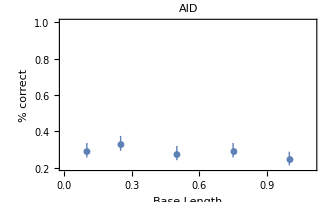
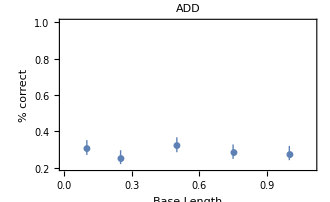
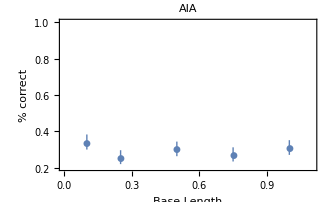
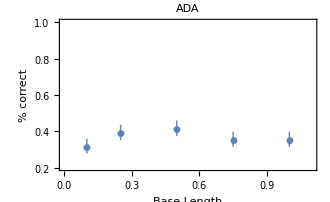
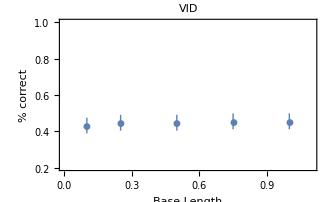
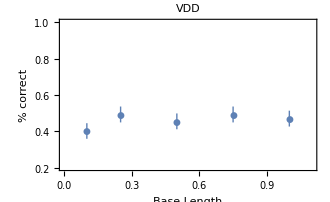
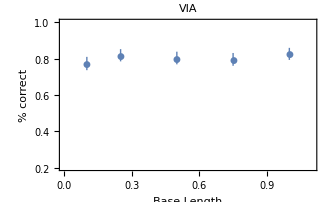
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,1.1},{0.2,1}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeAllNonExperts,{2}]),{2}]),{1}]
```

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,1.1},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@#[[-1]]}&,DataPerQTypeAll,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.3},0.2,1},{{PerHigh,0.8},0.4,1}]
```

Part::partd: Part specification DataPerQTypeAll⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAll⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Percent correct vs. Angle Size (decreasing on AID, ADD, AIA?,VDD // Increasing - VID, VIA))- Angles matter (not Euclidian!)

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,90},{0.2,1}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeAllNonExperts,{2}]),{2}]),{1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[ErrorListPlot[Evaluate@#,PlotRange->{{0,90},{PerLow,PerHigh}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size [deg]","% correct"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@#[[-1]]}&,DataPerQTypeAllNonExperts,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,0.2},0.2,1},{{PerHigh,0.8},0.4,1}]
```

Part::partd: Part specification DataPerQTypeAllNonExperts⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAllNonExperts⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,1.1},{0,30 10^3}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Time"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeAllExperts,{2}]),{2}]),{1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,1.1},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[2]],N@ToExpression@#[[3]]}&,DataPerQTypeAllExperts,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,15},8,40},{f,{Median,Mean}}]
```

Part::partd: Part specification DataPerQTypeAllExperts⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAllExperts⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

### Response times vs. Angle Size

```mathematica
(*1=angle; 2=base factor; 3=timing; 4=user answer; 5=correct/not*)
```

```mathematica
MapIndexed[ErrorListPlot[#1,PlotRange->{{0,90},{0,10 10^3}},PlotLabel->QuestionType[[#2[[1]]]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Time"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->330]&,(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@Median[#[[;;,2]]]},ErrorBar[N@MedianDeviation[#[[;;,2]]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeAllExperts,{2}]),{2}]),{1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[ErrorListPlot[#,PlotRange->{{0,90},{PerLow 10^3,PerHigh 10^3}},PlotLabel->QuestionType[[{i,j}]], Frame-> {True,True,False,False},FrameLabel->{"Angle Size","Response Times [ms]"},PlotStyle->Thick,PlotMarkers->Automatic,FrameStyle->16,ImageSize->600]&@(SortBy[#,First]&/@Map[{{ToExpression@#[[1,1]],N@f[#[[;;,2]]]},ErrorBar[N@MedianDeviation@#[[;;,2]]]}&,(GatherBy[#,First]&/@Map[{N@#[[1]],N@ToExpression@#[[3]]}&,DataPerQTypeAllExperts,{2}]),{2}])[[{i,j}]],{{i,1},1,8,1},{{j,2},1,8,1},{{PerLow,2},1,6},{{PerHigh,10},8,40},{f,{Median,Mean}}]
```

Part::partd: Part specification DataPerQTypeAllExperts⟦{1,2}⟧ is longer than depth of object.

Part::partd: Part specification QuestionType⟦{1,2}⟧ is longer than depth of object.

Part::partd: Part specification DataPerQTypeAllExperts⟦{1,2}⟧ is longer than depth of object.

ListPlot::lpn: DataPerQTypeAllExperts⟦{1,2}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

## Percent Correct vs. Education

```mathematica
PosOfSOME = 44;
Organized = Map[Sort,DataClean[[;;,1,;;]]];
WithoutSome = Delete[Organized, PosOfSOME];
EducationNum = WithoutSome[[;;,1]];
Graded = DataClnGraded[[;;,;;,-1]];
GradedWithoutSOME = Delete[Graded, PosOfSOME];

Totals = Map[Total, GradedWithoutSOME[[;;]]];
Totals = Map[Function[x,N@x/120], Totals];
EducationNumAndTotals = Transpose[{EducationNum,Totals}];
(*Now just need to graph this.*)
```

-Graphics-